```mathematica
rData = Import["D:\\Storage\\Вуз\\Задания\\Методы вычислений\\labs3kurs\\Interpolation_results\\polyvalues5.txt", "table"];
X = rData[[2]]
a =X[[1]]
b=X[[-1]]
Y = rData[[4]]
m=rData[[1]][[2]]

Points=rData[[6]]
Coeffs=rData[[8]]
n=rData[[7]][[2]]
L[x_]:=Evaluate[Coeffs[[1]]+Sum[Coeffs[[i]]Product[(y-Points[[k]]),{k,1,i-1}],{i,2,n}]]/.y->x;
(*f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;*)
(*f[x_]:=1/(1+25 x^2);*)
(*f[x_]:=1/ArcTan[1+10 x^2]*)
f[x_]:=Sin[π x];
Show[ListPlot[Table[{X[[i]],Y[[i]]},{i,m}],PlotStyle->{Red, PointSize[0.01]}],Plot[{f[x],L[x]},{x,a,b}]]
err1=Maximize[{Abs[L[x]-f[x]],a<=x<=b},x]
err2=MaximalBy[Table[{Abs[Y[[i]]-f[X[[i]]]],X[[i]]},{i,m}],First][[1]]
```

{-1,-0.98,-0.96,-0.94,-0.92,-0.9,-0.88,-0.86,-0.84,-0.82,-0.8,-0.78,-0.76,-0.74,-0.72,-0.7,-0.68,-0.66,-0.64,-0.62,-0.6,-0.58,-0.56,-0.54,-0.52,-0.5,-0.48,-0.46,-0.44,-0.42,-0.4,-0.38,-0.36,-0.34,-0.32,-0.3,-0.28,-0.26,-0.24,-0.22,-0.2,-0.18,-0.16,-0.14,-0.12,-0.1,-0.08,-0.06,-0.04,-0.02,0,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1}

-1

1

{-1.22465×10^-16,2.10013×10^13,-1.69949×10^11,9.23943×10^8,1.15807×10^7,-664659,16795,-87.9273,-20.5858,0.909443,-0.636086,-0.638737,-0.684205,-0.728996,-0.770513,-0.809017,-0.844328,-0.876307,-0.904827,-0.929776,-0.951057,-0.968583,-0.982287,-0.992115,-0.998027,-1,-0.998027,-0.992115,-0.982287,-0.968583,-0.951057,-0.929776,-0.904827,-0.876307,-0.844328,-0.809017,-0.770513,-0.728969,-0.684547,-0.637424,-0.587785,-0.535827,-0.481754,-0.425779,-0.368124,-0.309013,-0.248694,-0.187397,-0.12496,-0.0639425,0.000225218,0.0626555,0.137191,0.237284,0.638204,0.65089,6.96442,-20.7609,-43.6364,825.902,-1005.42,18430.3,36154.3,-831.614,179976,-4.03239×10^6,1.84952×10^7,3.91403×10^7,1.84141×10^8,8.20352×10^7,6.1392×10^8,1.18741×10^10,2.40041×10^9,1.50538×10^11,-3.42944×10^11,2.09935×10^11,-1.81451×10^13,-2.37106×10^13,-7.48902×10^14,-2.21201×10^15,5.78302×10^15,1.85441×10^16,1.61523×10^16,-3.62544×10^17,4.56433×10^18,-5.96706×10^18,-2.61155×10^19,4.76415×10^19,-4.15167×10^19,-9.62806×10^20,-2.81806×10^21,-4.14383×10^22,-5.92376×10^23,-3.50064×10^23,1.84719×10^24,-2.90347×10^24,-1.97923×10^25,1.12198×10^26,-5.06364×10^26,-6.47804×10^26,1.18021×10^28}

101

{-1,-0.984375,-0.96875,-0.953125,-0.9375,-0.921875,-0.90625,-0.890625,-0.875,-0.859375,-0.84375,-0.828125,-0.8125,-0.796875,-0.78125,-0.765625,-0.75,-0.734375,-0.71875,-0.703125,-0.6875,-0.671875,-0.65625,-0.640625,-0.625,-0.609375,-0.59375,-0.578125,-0.5625,-0.546875,-0.53125,-0.515625,-0.5,-0.484375,-0.46875,-0.453125,-0.4375,-0.421875,-0.40625,-0.390625,-0.375,-0.359375,-0.34375,-0.328125,-0.3125,-0.296875,-0.28125,-0.265625,-0.25,-0.234375,-0.21875,-0.203125,-0.1875,-0.171875,-0.15625,-0.140625,-0.125,-0.109375,-0.09375,-0.078125,-0.0625,-0.046875,-0.03125,-0.015625,0,0.015625,0.03125,0.046875,0.0625,0.078125,0.09375,0.109375,0.125,0.140625,0.15625,0.171875,0.1875,0.203125,0.21875,0.234375,0.25,0.265625,0.28125,0.296875,0.3125,0.328125,0.34375,0.359375,0.375,0.390625,0.40625,0.421875,0.4375,0.453125,0.46875,0.484375,0.5,0.515625,0.53125,0.546875,0.5625,0.578125,0.59375,0.609375,0.625,0.640625,0.65625,0.671875,0.6875,0.703125,0.71875,0.734375,0.75,0.765625,0.78125,0.796875,0.8125,0.828125,0.84375,0.859375,0.875,0.890625,0.90625,0.921875,0.9375,0.953125,0.96875,0.984375,1}

{-1.22465×10^-16,-3.14033,0.242091,5.15216,-0.397664,-2.52972,0.195805,0.590037,-0.0459881,-0.0791897,0.00347438,-0.0331054,0.831716,-8.69676,60.6474,-252.518,-185.416,14323.7,-149760,1.00097×10^6,-4.47102×10^6,7.22319×10^6,9.82093×10^7,-1.32153×10^9,1.05154×10^10,-6.57876×10^10,3.47542×10^11,-1.58683×10^12,6.25759×10^12,-2.07076×10^13,5.18443×10^13,-5.10703×10^13,-4.32578×10^14,3.8768×10^15,-2.12518×10^16,9.47901×10^16,-3.70106×10^17,1.30266×10^18,-4.1898×10^18,1.23843×10^19,-3.36384×10^19,8.34291×10^19,-1.85796×10^20,3.56655×10^20,-5.21414×10^20,2.34623×10^20,2.12678×10^21,-1.14588×10^22,4.10158×10^22,-1.24256×10^23,3.41997×10^23,-8.85053×10^23,2.20195×10^24,-5.35587×10^24,1.29004×10^25,-3.10283×10^25,7.47633×10^25,-1.80182×10^26,4.32245×10^26,-1.02589×10^27,2.39518×10^27,-5.47636×10^27,1.22253×10^28,-2.66023×10^28,5.63952×10^28,-1.1651×10^29,2.34797×10^29,-4.62199×10^29,8.90223×10^29,-1.68067×10^30,3.11572×10^30,-5.68109×10^30,1.02018×10^31,-1.80593×10^31,3.15278×10^31,-5.42809×10^31,9.21199×10^31,-1.53977×10^32,2.53212×10^32,-4.09172×10^32,6.48869×10^32,-1.00849×10^33,1.53422×10^33,-2.28168×10^33,3.31288×10^33,-4.68968×10^33,6.46229×10^33,-8.65196×10^33,1.12271×10^34,-1.4073×10^34,1.69573×10^34,-1.94925×10^34,2.11024×10^34,-2.09967×10^34,1.81617×10^34,-1.13754×10^34,-7.47803×10^32,1.9676×10^34,-4.68426×10^34,8.34954×10^34,-1.30521×10^35,1.8826×10^35,-2.56332×10^35,3.33491×10^35,-4.17545×10^35,5.05356×10^35,-5.92928×10^35,6.75617×10^35,-7.48435×10^35,8.06434×10^35,-8.45152×10^35,8.61065×10^35,-8.51996×10^35,8.17429×10^35,-7.58692×10^35,6.78956×10^35,-5.83044×10^35,4.77063×10^35,-3.67867×10^35,2.6243×10^35,-1.67174×10^35,8.73322×10^34,-2.64288×10^34,-1.40663×10^34,3.48689×10^34,-3.87733×10^34,3.03206×10^34,-1.52797×10^34,0}

129

```mathematica
f[0.98]
```

```mathematica
0.06279051952931358
0.0627905
0.0526038
```

```mathematica
D[f[x],{x,n+1}]
```

-π^34 Sin[π x]

```mathematica
n
```

33

```mathematica
Y[[n]]
```

0.770513

```mathematica
errT={0,0,0,0,0};
```

```mathematica
errT[[4]]=err2[[1]]
```

0.0101867

```mathematica
errT
```

{0.00120812,0.0000456446,0.0000898038,0.0101867,0}

{1.8117,{x→0.967152}}

-1

1

{-1.22465×10^-16,-0.0626498,-0.125064,-0.187009,-0.248249,-0.308548,-0.367673,-0.425387,-0.481456,-0.535645,-0.587719,-0.637442,-0.684581,-0.728901,-0.770239,-0.808492,-0.843564,-0.875358,-0.903776,-0.928721,-0.950095,-0.967801,-0.981742,-0.99182,-0.997939,-1,-0.997939,-0.99182,-0.981742,-0.967801,-0.950095,-0.928721,-0.903776,-0.875358,-0.843564,-0.808492,-0.770239,-0.728901,-0.684581,-0.637442,-0.587719,-0.535645,-0.481456,-0.425387,-0.367673,-0.308548,-0.248249,-0.187009,-0.125064,-0.0626498,-4.16334×10^-17,0.0626498,0.125064,0.187009,0.248249,0.308548,0.367673,0.425387,0.481456,0.535645,0.587719,0.637442,0.684581,0.728901,0.770239,0.808492,0.843564,0.875358,0.903776,0.928721,0.950095,0.967801,0.981742,0.99182,0.997939,1,0.997939,0.99182,0.981742,0.967801,0.950095,0.928721,0.903776,0.875358,0.843564,0.808492,0.770239,0.728901,0.684581,0.637442,0.587719,0.535645,0.481456,0.425387,0.367673,0.308548,0.248249,0.187009,0.125064,0.0626498,9.71445×10^-17}

101

{-1,-0.75,-0.5,-0.25,0,0.25,0.5,0.75,1}

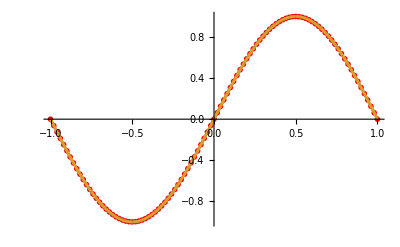

{0.00106607,{x→-0.370945}}

```mathematica
rData2 = Import["D:\\Storage\\Вуз\\Задания\\Методы вычислений\\labs3kurs\\Interpolation_results\\splinevalues1.txt", "table"];
X2 = rData2[[2]];
a2 =X2[[1]]
b2=X2[[-1]]
Y2 = rData2[[4]]
m2=rData2[[1]][[2]]

Points2=rData2[[6]]
CoA=rData2[[8]];
CoB=rData2[[10]];
CoC=rData2[[12]];
CoD=rData2[[14]];
n2=rData2[[7]][[2]];
S[x_]:=Piecewise[Table[{CoA[[i]]+CoB[[i]](x-Points2[[i]])+CoC[[i]](x-Points2[[i]])^2+CoD[[i]](x-Points2[[i]])^3,Points2[[i]]<=x<=Points2[[i+1]]},{i,n2}],x];
(*f[x_]:=1/ArcTan[1+10 x^2];*)
(*f[x_]:=(4 x^3+2 x^2−4x+2)^(√2)+ArcSin[1/(5+x-x^2)]-5;
f[x_]:=1/(1+25 x^2);*)
(*f[x_]:=x^2;*)
f[x_]:=Sin[π x];
Show[ListPlot[Table[{X2[[i]],Y2[[i]]},{i,m2}],PlotStyle->{Red, PointSize[0.01]}],Plot[{f[x],S[x]},{x,a2,b2}]]
err1=Maximize[{Abs[S[x]-f[x]],a<=x<=b},x]
err2=MaximalBy[Table[{X2[[i]],Abs[Y2[[i]]-f[X2[[i]]]]},{i,m2}],Last]
```

```mathematica
S[x]
```

Piecewise[{{x, -1≤x≤-0.5}, {0.+x, -0.5≤x≤0}, {x, 0≤x≤0.5}, {0.+x, 0.5≤x≤1}, {x, True}}]